```mathematica
1/Sqrt[2 Pi]Integrate[Exp[-x^2/2],{x,-r,r}]
```

Erf[r/(√2)]

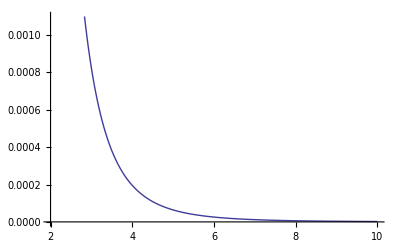

```mathematica
Plot[NIntegrate[1/(1+x^6),{x,r,Infinity}],{r,2,10}]
```

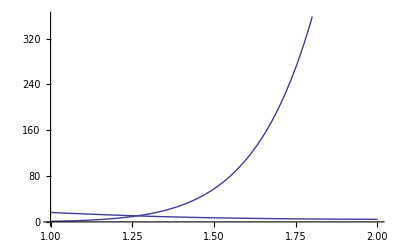

```mathematica
Plot[{20Exp[x^2/2]/(1+x^p),x^q}/.{p->5,q->10},{x,1,2}]
```

```mathematica
Integrate[x^1/(1+x^2),{x,3,Infinity}]
```

Integrate::idiv: Integral of x/1 + x^2 does not converge on {3, ∞}.

∫_3^∞ x/(1+x^2)ⅆx

```mathematica
N[Reduce[{ x^10==Exp[x^2/2]/(1+x^2),x>0},x]]
N[Reduce[{24 Log[x]==x^2,x>0},x]]
```

x==0.980888||x==6.78101

x==1.04671||x==6.77671

```mathematica
Normal[Series[Exp[x^2/2]/(1+x^2),{x,0,20}]]
```

1-x^2/2+(5 x^4)/8-(29 x^6)/48+(233 x^8)/384-(2329 x^10)/3840+(27949 x^12)/46080-(78257 x^14)/129024+(6260561 x^16)/10321920-(112690097 x^18)/185794560+(2253801941 x^20)/3715891200

```mathematica
Series[Log[1+x^2],{x,0,10}]
```

x^2-x^4/2+x^6/3-x^8/4+x^10/5+O[x]^11

```mathematica
N[Reduce[Log[x]==x^2/2,x]]
```

x==0.91997-0.726782 ⅈ||x==0.91997+0.726782 ⅈ

```mathematica
N[Log[2]]
```

0.693147

```mathematica
N[Reduce[Normal[x^12-Series[Exp[x^2/2],{x,0,24}]]==0,x]]
```

x==0.-10.7477 ⅈ||x==0.+10.7477 ⅈ||x==0.-0.962161 ⅈ||x==0.+0.962161 ⅈ||x==-1.04671||x==1.04671||x==-10.3627||x==10.3627||x==-5.21443+9.32188 ⅈ||x==5.21443-9.32188 ⅈ||x==-5.21443-9.32188 ⅈ||x==5.21443+9.32188 ⅈ||x==-0.460716+0.862767 ⅈ||x==0.460716-0.862767 ⅈ||x==-0.460716-0.862767 ⅈ||x==0.460716+0.862767 ⅈ||x==-0.861771+0.543444 ⅈ||x==0.861771-0.543444 ⅈ||x==-0.861771-0.543444 ⅈ||x==0.861771+0.543444 ⅈ||x==-9.00016+5.40666 ⅈ||x==9.00016-5.40666 ⅈ||x==-9.00016-5.40666 ⅈ||x==9.00016+5.40666 ⅈ

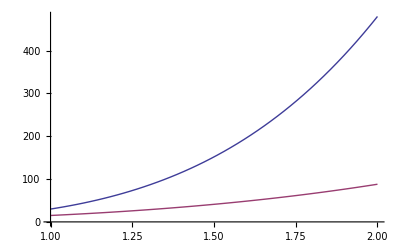

```mathematica
Plot[{30x^4,x^4+4x^3+10x^2},{x,1,2}]
```

```mathematica
N[Integrate[300x^10 Exp[-x^2/2],{x,7,Infinity}]]
```

0.336173

```mathematica
1/Sqrt[2 Pi]Integrate[1/(1+x^2),{x,r,Infinity}]
```

If[r>0,ArcTan[1/r],Integrate[1/(1+x^2),{x,r,∞},Assumptions→r≤0]]/(√(2 π))

```mathematica
(r^(1-p) Hypergeometric2F1[1,(-1+p)/p,2-1/p,-r^-p])/(-1+p)
```

```mathematica
Simplify[1/Sqrt[2Pi]Integrate[x^0 Exp[-x^2/2],{x,r,Infinity}]]
```

1/2 Erfc[r/(√2)]

```mathematica
2^(1/2 (-1+p)) (r^2)^(1/2 (-1-p)) ((-r^(1+p)+(r^2)^((1+p)/2)) Gamma[(1+p)/2]+r^(1+p) Gamma[(1+p)/2,r^2/2])
```

1.-0.5 x^2+0.375 x^4-0.3125 x^6+0.273438 x^8-0.246094 x^10+0.225586 x^12-0.209473 x^14+0.196381 x^16-0.185471 x^18+0.176197 x^20

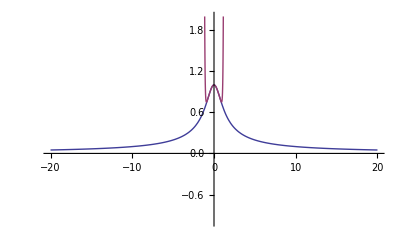

(ⅇ^(1/4) BesselK[0,1/4])/(√(2 π))

0.78964

```mathematica
y=N[Normal[Series[1/Sqrt[(1+x^2)],{x,0,20}]]]
Plot[{1/Sqrt[(1+x^2)],y},{x,-20,20},PlotRange->{{-20,20},{-1,2}}]
1/Sqrt[2 Pi]Integrate[1/Sqrt[(1+x^2) ]Exp[-x^2/2],{x,-Infinity,Infinity}]
```

1-x^2+x^4-x^6+x^8-x^10

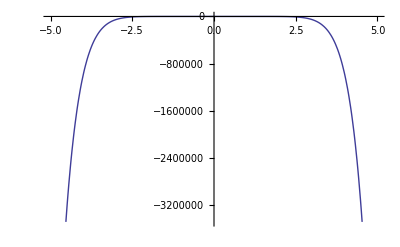

1-x^2+x^4-x^6+x^8-x^10

```mathematica
y=Normal[Series[1/(1+x^2),{x,0,10}]]
Plot[y,{x,-5,5}]
Normal[Series[1/(1+x^2),{x,0,10}]]
```

```mathematica
0.7978845608028654
d=0.3381;
r=5;
CC=2.3164;
p=5;

d(Erf[r/Sqrt[2]]+1)+4CC/Sqrt[2 Pi] Integrate[x^p Exp[-x^2/2],{x,r,Infinity}]
```

0.797885

0.686297

```mathematica
N[1/Sqrt[2 Pi]Integrate[Abs[x]Exp[-x^2/2],{x,-Infinity,Infinity}]]
2/Sqrt[2 Pi]Integrate[x Exp[-x^2/2],{x,0,Infinity}]
```

0.797885

√(2/π)